```mathematica
Clear[xi,h,yj]
$Assumptions={h>0&&xi∈Reals&&yj∈Reals};
ϕh[x_,y_,xi_,yj_]:=Piecewise[{{1+2/h(x-xi-h/2)+2/h(y-yj-h/2), y≥yj&&x≥xi&&y-yj-h≤-(x-xi)}, {1-2/h(x-xi-h/2)-2/h(y-yj-h/2), y<=yj+h&&x<=xi+h&&y-yj-h>=-(x-xi)}, {0, True}}]
ϕl1[x_,y_,xi_,yj_]:=Piecewise[{{1-2/h(y-yj), y≥yj&&x≥xi&&y-yj-h≤-(x-xi)}, {1+2/h(y-yj), y<=yj&&x<=xi+h&&y-yj>=-(x-xi)}, {0, True}}]
ϕl2[x_,y_,xi_,yj_]:=Piecewise[{{1-2/h(x-xi), y≥yj&&x≥xi&&y-yj-h≤-(x-xi)}, {1+2/h(x-xi), y<=yj+h&&x<=xi&&y-yj>=-(x-xi)}, {0, True}}]
gradϕh[x_,y_,xi_,yj_]:=Piecewise[{{{2/h,2/h}, y≥yj&&x≥xi&&y-yj-h≤-(x-xi)}, {{-2/h,-2/h}, y<=yj+h&&x<=xi+h&&y-yj-h>=-(x-xi)}, {{0,0}, True}}]
gradϕl1[x_,y_,xi_,yj_]:=Piecewise[{{{0,-2/h}, y≥yj&&x≥xi&&y-yj-h≤-(x-xi)}, {{0,2/h}, y<=yj&&x<=xi+h&&y-yj>=-(x-xi)}, {{0,0}, True}}]
gradϕl2[x_,y_,xi_,yj_]:=Piecewise[{{{-2/h,0}, y≥yj&&x≥xi&&y-yj-h≤-(x-xi)}, {{2/h,0}, y<=yj+h&&x<=xi&&y-yj>=-(x-xi)}, {{0,0}, True}}]
ϕh[xi+h/2,yj+h/2,xi,yj]==1&&
ϕh[xi+h/2,yj,xi,yj]==0&&
ϕh[xi+h/2,yj+h,xi,yj]==0&&
ϕh[xi,yj+h/2,xi,yj]==0&&
ϕh[xi+h,yj+h/2,xi,yj]==0&&
ϕl[xi+h/2,yj,xi,yj]==1&&
ϕl[xi,yj+h/2,xi,yj]==0&&
ϕl[xi+h/2,yj+h/2,xi,yj]==0&&
ϕl[xi+h,yj-h/2,xi,yj]==0&&
ϕl[xi+h/2,yj-h/2,xi,yj]==0//FullSimplify;
Integrate[gradϕh[x,y,xi,yj].gradϕh[x,y,xi,yj],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

8

```mathematica
Integrate[gradϕh[x,y,xi,yj].gradϕl1[x,y,xi,yj],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

-2

```mathematica
Integrate[gradϕh[x,y,xi,yj].gradϕl1[x,y,xi,yj+h],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

-2

```mathematica
Integrate[gradϕh[x,y,xi,yj].gradϕl2[x,y,xi,yj],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

-2

```mathematica
Integrate[gradϕh[x,y,xi,yj].gradϕl2[x,y,xi+h,yj],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

-2

```mathematica
Integrate[gradϕl1[x,y,xi,yj].gradϕl1[x,y,xi,yj],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

4

```mathematica
Integrate[gradϕl2[x,y,xi,yj].gradϕl2[x,y,xi,yj],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

4

```mathematica
Integrate[gradϕl1[x,y,xi,yj].gradϕl2[x,y,xi,yj],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

0

```mathematica
Integrate[gradϕl1[x,y,xi,yj].gradϕl2[x,y,xi+h,yj-h],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

0

```mathematica
Integrate[gradϕl1[x,y,xi,yj].gradϕl2[x,y,xi,yj],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

0

```mathematica
gradϕl1[x,y,xi,yj].gradϕl2[x,y,xi,yj]//FullSimplify
```

0

```mathematica
gradϕl1[x,y,xi,yj].gradϕl2[x,y,xi+h,yj-h]//FullSimplify
```

0

```mathematica
h = 1;
Plot3D[{ϕl1[x,y,0,0],ϕl2[x,y,0,0],ϕl2[x,y,h,-h]},{x,-1,1},{y,-1,1},PlotRange->All]
```

-Graphics3D-

```mathematica
h=1;
Plot3D[{gradϕl2[x,y,0,0]},{x,-1,1},{y,-1,1},PlotRange->All]
```

-Graphics3D-

```mathematica
gradϕh[x,y].gradϕh[x,y]//FullSimplify
```

Piecewise[{{8/h^2, (x≥xi&&y≥yj&&h+xi+yj≥x+y)||(h+xi+yj≤x+y&&h+xi≥x&&h+yj≥y)}, {0, True}}]

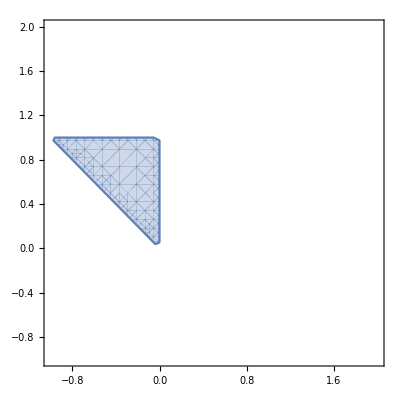

```mathematica
yj = 0;
xi = 0;
h = 1;
RegionPlot[y<=yj+h&&x<=xi&&y-yj>=-(x-xi),{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

```mathematica
ϕh[xi+h/2,yj]
```

0

```mathematica
ϕh[xi+h,yj+h]
```

-1

```mathematica
Plot3D[ϕl2[x,y,xi,yj],{x,xi-h,xi+2h},{y,yj-h,yj+2h}]
```

-Graphics3D-

```mathematica
Integrate[,{x,]
```